## Neutrino, photon temperatures T_(ν,γ) and scale factor a dynamics

### Importing data

```mathematica
(* Load the corrections to the rates as a result of a non-negligible electron mass *)
SetDirectory[NotebookDirectory[]];
FacMeVtos1=1/(6.58212*10^-16* 10^-6); 
Clear[geL,geR,gμL,gμR,fannνe,fscaνe,fannνμ,fscaνμ,fscanνe,fscanνμ];
data=Import["SM_Rates/nue_ann.dat","Table",HeaderLines-> 1];
fannνe=Interpolation[data];
data=Import["SM_Rates/nue_scatt.dat","Table",HeaderLines-> 1];
fscaνe=Interpolation[data];
data=Import["SM_Rates/numu_ann.dat","Table",HeaderLines-> 1];
fannνμ=Interpolation[data];
data=Import["SM_Rates/numu_scatt.dat","Table",HeaderLines-> 1];
fscaνμ=Interpolation[data];
data=Import["SM_Rates/sigmav_nue.dat","Table",HeaderLines-> 1];
fscanνe=Interpolation[data];
data=Import["SM_Rates/sigmav_numu.dat","Table",HeaderLines-> 1];
fscanνμ=Interpolation[data];

(* Uncomment if one wants to consider me = 0 in the rates *)
(*Clear[fannνe,fscaνe,fannνμ,fscaνμ,fscanνe,fscanνμ]
fannνe[x_]:=1;fscaνe[x_]:=1;fannνμ[x_]:=1;fscaνμ[x_]:=1;fscanνe[x_]:=1;fscanνμ[x_]:=1;*)

(* Spin-Statistics Corrections to the MB interaction rates. Set to 1 for the MB case *)
faFD = 0.884;fsFD = 0.829;fnFD = 0.852;

(* Low energy couplings desciribin NC and CC interactions of neutrinos and electrons *)
(* See Table 10.3 of the EW review of the PDG and Table 6 of 1303.5522  *)
geL=0.727;geR=0.233;gμL=-0.273;gμR=0.233;

Func[T1_,T2_,μ1_,μ2_]:=32 *faFD*(Exp[2 μ1/T1] T1^9-Exp[2 μ2/T2] T2^9)+ 56 *fsFD*T1^4 T2^4 Exp[μ1/T1]Exp[μ2/T2]*(T1-T2);

(* Energy Density Transfer Rates: δρ/δt *)
ΔρSMνe[Tγ_,Tνe_,Tνμ_,Tντ_,μνe_,μνμ_]:=  GF^2/π^5(4 *(geL^2+geR^2)(32*faFD*fannνe[Tγ]*(Tγ^9-Exp[2 μνe/Tνe] Tνe^9)+56*fsFD* Tγ^4 *Tνe^4*fscaνe[Tγ]*Exp[μνe/Tνe]*(Tγ-Tνe))+Func[Tνμ,Tνe,μνμ,μνe]+Func[Tντ,Tνe,0,μνe])/.GF-> 1.1663787 10^-11;
ΔρSMνμ[Tγ_,Tνe_,Tνμ_,Tντ_,μνe_,μνμ_]:=  GF^2/π^5(4 *(gμL^2+gμR^2)(32*faFD*fannνμ[Tγ]*(Tγ^9-Exp[2 μνμ/Tνμ] Tνμ^9)+56 *fsFD*Tγ^4 *Tνμ^4*fscaνμ[Tγ]*Exp[μνμ/Tνμ]*(Tγ-Tνμ))+Func[Tνe,Tνμ,μνe,μνμ]+Func[Tντ,Tνμ,0,μνμ])/.GF-> 1.1663787 10^-11;
ΔρSMντ[Tγ_,Tνe_,Tνμ_,Tντ_,μνe_,μνμ_]:=  GF^2/π^5(4 *(gμL^2+gμR^2)(32*faFD*fannνμ[Tγ]*(Tγ^9-Exp[2 μνμ/Tντ] Tντ^9)+56 *fsFD*Tγ^4 *Tντ^4*fscaνμ[Tγ]*Exp[μνμ/Tντ]*(Tγ-Tντ))+Func[Tνe,Tντ,μνe,0]+Func[Tνμ,Tντ,μνμ,0])/.GF-> 1.1663787 10^-11;
```

### Evolution equation for the energy densities

```mathematica
TransferFactor[T1_,T2_]=(32*0.884*Cancel[(T1^9-T2^9)/(T1-T2)]+56*0.829*T1^4*T2^4)(T1-T2);
(*A toy factor that effectively takes into account the effect of non-perfect FD spectrum of neutrinos on the EM<->ν equilibration (see long BBN draft for details)*)
Rratio=(*0.8*)1;
(*Rates of energy density transfer between EM and Subscript[ν, e,μ,τ] sectors. Neutrino oscillations are taken into account*)
ΓEMνEqEM[Tγ_,Tνe_,Tνμ_,Tντ_]=10^-15*ΔρSMνe[10^3*Tγ,10^3*Tνe,10^3*Tνμ,10^3*Tντ,0,0]+ΔρSMνμ[Tγ*10^3,Tνe*10^3,Tνμ*10^3,Tντ*10^3,0,0]*10^-15+ΔρSMντ[Tγ*10^3,Tνe*10^3,Tνμ*10^3,Tντ*10^3,0,0]*10^-15;(*Rratio GFvalue^2/Pi^5((1+4*sinθW2+8*sinθW2^2)*TransferFactor[Tγ,Tνe]+(1-4*sinθW2+8*sinθW2^2)*(TransferFactor[Tγ,Tνμ]+TransferFactor[Tγ,Tντ]));*)
ΓEMνEqνePure[Tγ_,Tνe_,Tνμ_,Tντ_]=ΔρSMνe[10^3*Tγ,10^3*Tνe,10^3*Tνμ,10^3*Tντ,0,0]*10^-15;
(*GFvalue^2/Pi^5(Rratio*TransferFactor[Tγ,Tνe](1+4*sinθW2+8*sinθW2^2)+TransferFactor[Tνμ,Tνe]+TransferFactor[Tντ,Tνe]);*)
ΓEMνEqνμPure[Tγ_,Tνe_,Tνμ_,Tντ_]=ΔρSMνμ[Tγ*10^3,Tνe*10^3,Tνμ*10^3,Tντ*10^3,0,0]*10^-15;(*GFvalue^2/Pi^5(Rratio*TransferFactor[Tγ,Tνμ](1-4*sinθW2+8*sinθW2^2)+TransferFactor[Tνe,Tνμ]+TransferFactor[Tντ,Tνμ]);*)
ΓEMνEqντPure[Tγ_,Tνe_,Tνμ_,Tντ_]=ΔρSMντ[Tγ*10^3,Tνe*10^3,Tνμ*10^3,Tντ*10^3,0,0]*10^-15;(*GFvalue^2/Pi^5(Rratio*TransferFactor[Tγ,Tντ](1-4*sinθW2+8*sinθW2^2)+TransferFactor[Tνe,Tντ]+TransferFactor[Tνμ,Tντ]);*)
ΓEMνEqνe[Tγ_,Tνe_,Tνμ_,Tντ_]=(PeeInt[10^3 Tγ]*ΓEMνEqνePure[Tγ,Tνe,Tνμ,Tντ]+PeμInt[10^3 Tγ]*ΓEMνEqνμPure[Tγ,Tνe,Tνμ,Tντ]+PeτInt[10^3 Tγ]*ΓEMνEqντPure[Tγ,Tνe,Tνμ,Tντ]);
ΓEMνEqνμ[Tγ_,Tνe_,Tνμ_,Tντ_]=(PμeInt[10^3 Tγ]*ΓEMνEqνePure[Tγ,Tνe,Tνμ,Tντ]+PμμInt[10^3 Tγ]*ΓEMνEqνμPure[Tγ,Tνe,Tνμ,Tντ]+PμτInt[10^3 Tγ]*ΓEMνEqντPure[Tγ,Tνe,Tνμ,Tντ]);
ΓEMνEqντ[Tγ_,Tνe_,Tνμ_,Tντ_]=(PτeInt[10^3 Tγ]*ΓEMνEqνePure[Tγ,Tνe,Tνμ,Tντ]+PτμInt[10^3 Tγ]*ΓEMνEqνμPure[Tγ,Tνe,Tνμ,Tντ]+PττInt[10^3 Tγ]*ΓEMνEqντPure[Tγ,Tνe,Tνμ,Tντ]);
(*Dynamics of neutrino, photon temperatures and scale factor in presence of decays of HNLs. It is assumed that decaying HNLs store exactly 1/3 of their neutrino energy into each neutrino flavor energy*)
TγDynamics[Tγ_,Tνe_,Tνμ_,Tντ_,ρX_,ξinjEM_,τX_,mX_]=-sToGeVminusOne*((4*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]*ργ[Tγ]+3*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]*(ρe[Tγ]+pe[Tγ]))/(DρeDT[Tγ]+DργDT[Tγ]))-sToGeVminusOne*ΓEMνEqEM[Tγ,Tνe,Tνμ,Tντ]/(DρeDT[Tγ]+DργDT[Tγ])+(ρX*ξinjEM)/(τX*(DρeDT[Tγ]+DργDT[Tγ]));
TνeDynamics[Tγ_,Tνe_,Tνμ_,Tντ_,ρX_,ξinjνe_,τX_,mX_]=-sToGeVminusOne*(4*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]*ρνα[Tνe])/dρναdT[Tνe]+sToGeVminusOne*ΓEMνEqνe[Tγ,Tνe,Tνμ,Tντ]/dρναdT[Tνe]+(ρX*(ξinjνe))/(τX*dρναdT[Tνe]);
TνμDynamics[Tγ_,Tνe_,Tνμ_,Tντ_,ρX_,ξinjνμ_,τX_,mX_]=-sToGeVminusOne*(4*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]ρνα[Tνμ])/dρναdT[Tνμ]+sToGeVminusOne*ΓEMνEqνμ[Tγ,Tνe,Tνμ,Tντ]/dρναdT[Tνμ]+(ρX*(ξinjνμ))/(τX*dρναdT[Tνμ]);
TντDynamics[Tγ_,Tνe_,Tνμ_,Tντ_,ρX_,ξinjντ_,τX_,mX_]=-sToGeVminusOne*(4*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]ρνα[Tντ])/dρναdT[Tντ]+sToGeVminusOne*ΓEMνEqντ[Tγ,Tνe,Tνμ,Tντ]/dρναdT[Tντ]+(ρX*(ξinjντ))/(τX*dρναdT[Tντ]);
ρXdynamicsMattDom[Tγ_,Tνe_,Tνμ_,Tντ_,ρX_,τX_,mX_]=-ρX/τX-3*sToGeVminusOne*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX]ρX;
aRatioDynamics[Tγ_,Tνe_,Tνμ_,Tντ_,aRatio_,ρX_]=aRatio*sToGeVminusOne*HInGeVρ[Tγ,Tνe,Tνμ,Tντ,ρX];
```

## System of equations

### System

```mathematica
SCALETγ=(*10^-3*)1;
EqsEqTemp[mX_,τX_,nXini_,ξEM_,ξνe_,ξνμ_,ξντ_,tIni_,Tini_]={D[Tγ[t]SCALETγ,t]==TγDynamics[Tγ[t]SCALETγ,Tνe[t]SCALETγ,Tνμ[t]SCALETγ,Tντ[t]SCALETγ,If[t<20τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatio[t],t,tIni]],0.],ξEM,τX,mX],D[Tνe[t]SCALETγ,t]==TνeDynamics[Tγ[t]SCALETγ,Tνe[t]SCALETγ,Tνμ[t]SCALETγ,Tντ[t]SCALETγ,If[t<20τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatio[t],t,tIni]],0.],ξνe,τX,mX],
D[Tνμ[t]SCALETγ,t]==TνμDynamics[Tγ[t]SCALETγ,Tνe[t]SCALETγ,Tνμ[t]SCALETγ,Tντ[t]SCALETγ,If[t<20τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatio[t],t,tIni]],0.],ξνμ,τX,mX],D[Tντ[t]SCALETγ,t]==TντDynamics[Tγ[t]SCALETγ,Tνe[t]SCALETγ,Tνμ[t]SCALETγ,Tντ[t]SCALETγ,If[t<20τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatio[t],t,tIni]],0.],ξντ,τX,mX],D[aRatio[t],t]==aRatioDynamics[Tγ[t]SCALETγ,Tνe[t]SCALETγ,Tνμ[t]SCALETγ,Tντ[t]SCALETγ,aRatio[t],If[t<20τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatio[t],t,tIni]],0.]],Tγ[tIni]SCALETγ==Tini,Tνe[tIni]SCALETγ==TiniEM,Tνμ[tIni]SCALETγ==TiniEM,Tντ[tIni]SCALETγ==TiniEM,aRatio[tIni]==1};
```

### Solution

```mathematica
Tmax=6*10^-3;
TiniEM=20.*10^-3;
TAAE[mass_]=0.05*10^-3;
tmaxsol=1000;
DynamicsTimeScaleFactorNumberDens[mX_,τX_,nXini_,ξEM_,ξνe_,ξνμ_,ξντ_,tmax_]:=Module[{mass=mX,lifetime=τX,tvals,tablepars,ρXin,EqsEq,tIniEM,nXt,tT,Tt,aRatiot,aRatioT,ηBt,ηBT,Ht,HT,Tγt,ρXt,ρXT,solUniverse,Tνet,TνeT,TνμT,Tνμt,TντT,Tντt},
ρXin=nXini*mX;
tIniEM=tInSinTermsOfTinMeVsimple[10^3 TiniEM,10.75+ρXin/(Pi^2/30*TiniEM^4)];
EqsEq=EqsEqTemp[mX,τX,nXini,ξEM,ξνe,ξνμ,ξντ,tIniEM,TiniEM];
solUniverse=NDSolve[Rationalize[EqsEq,0],{Tγ,Tνe,Tνμ,Tντ,aRatio},{t,tIniEM,1.3*tmax},MaxSteps->50000,Method->{"BDF","MaxDifferenceOrder"->2}][[1]];
Tγt[t_]=Tt[t_]=SCALETγ(Tγ[t]/.solUniverse);
Tνet[t_]=SCALETγ(Tνe[t]/.solUniverse);
Tνμt[t_]=SCALETγ(Tνμ[t]/.solUniverse);
Tντt[t_]=SCALETγ(Tντ[t]/.solUniverse);
aRatiot=aRatio/.solUniverse;
tvals=Join[Table[10^t,{t,Log10[tIniEM],Log10[tmax],0.005}],{tmax}];
tablepars=Join[Table[{10^t,aRatiot[10^t],Tγt[10^t],Tνet[10^t],Tνμt[10^t],Tντt[10^t]},{t,Log10[tIniEM],Log10[tmax],0.005}],{{tmax,aRatiot[tmax],Tγt[tmax],Tνet[tmax],Tνμt[tmax],Tντt[tmax]}}];
tT[T_]=Interpolation[tablepars[[All,{3,1}]],InterpolationOrder->1][T];
aRatioT[T_]=Interpolation[SortBy[tablepars[[All,{3,2}]],#[[1]]&],InterpolationOrder->1][T];
ηBt[t_]=ηBPlanck*((aRatiot[t]*Tt[t])/(aRatiot[tmaxsol]*Tt[tmaxsol]))^-3;
ηBT[T_]=ηBPlanck*((aRatioT[T]T)/(Tt[tmaxsol]*aRatiot[tmaxsol]))^-3;
ρXt[t_]=If[t<20*τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatiot[t],t,tIniEM]],0.];
ρXT[T_]=If[tT[T]<20*τX,Evaluate[ρLLPscaling[mX,nXini,τX,aRatioT[T],tT[T],tIniEM]],0.];
nXt[t_]=ρXt[t]/mX;
{TνeT[T_],TνμT[T_],TντT[T_]}=Interpolation[tablepars[[All,{3,#}]],InterpolationOrder->1][T]&/@{-3,-2,-1};
Ht[t_]=Interpolation[Table[{t,HInGeVρ[Tt[t],Tνet[t],Tνμt[t],Tντt[t],ρXt[t]]},{t,tvals}],InterpolationOrder->1][t]*sToGeVminusOne;
HT[T_]=Interpolation[Table[{T,HInGeVρ[T,TνeT[T],TνμT[T],TντT[T],ρXT[T]]},{T,tablepars[[All,3]]}],InterpolationOrder->1][T]*sToGeVminusOne;
(*tTtemp[T_]:=Quiet[t/.FindRoot[Tγtemp[t]==T,{t,3*tIniEM,tIniEM,1.3*tmax}][[1]]];*)
{Join[{nXt[t],tT[T],Tt[t],aRatiot[t],aRatioT[T],ηBt[t],ηBT[T],Ht[t],HT[T],Tνet[t],TνeT[T],Tνμt[t],TνμT[T],Tντt[t],TντT[T]}],tIniEM}
]
DynamicsTimeScaleFactorNumberDens[mX_,τX_,nXini_,ξEM_,tmax_]:=Module[{},
DynamicsTimeScaleFactorNumberDens[mX,τX,nXini,ξEM,(1-ξEM)/3,(1-ξEM)/3,(1-ξEM)/3,tmax]
]
```

Critical value of r_2 obtained from r_2/(1 - SubscriptBox[r, 2]) = (ρ_(ν, SM))/(ρ_(EM, SM)) (at T ~ MeV) = 21/22:

21/43

Ratio r_1: 0.834156

Ratio r_1: 0.816355

Ratio r_1: 0.967653

Ratio r_1: 0.959938

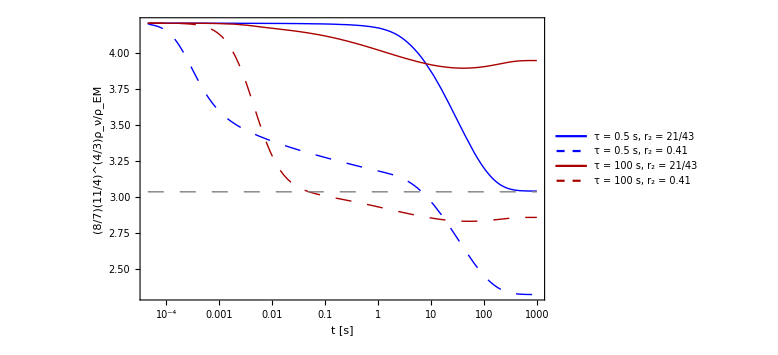

```mathematica
(*Print["Critical value of r_2 obtained from r_2/(1 - SubscriptBox[r, 2]) = (ρ_(ν, SM))/(ρ_(EM, SM)) (at T ~ MeV) = 21/22:"]
r2critical=r2/.Solve[r2/(1-r2)==21/22,r2][[1]]
ξEMtest=(*1-r2critical*)0.6;
BlockTest[nXini_,mXtest_,τXtest_,ξEMtest_]:=Block[{},
fff1[t_]=DynamicsTimeScaleFactorNumberDens[mXtest,τXtest,nXini,ξEMtest,(1-ξEMtest)/3,(1-ξEMtest)/3,(1-ξEMtest)/3,tmaxsol];
{{nXtsol[t_],tTsol[T_],Ttsol[t_],aRatiotsol[t_],aRatioTsol[T_],ηBtsol[t_],ηBTsol[T_],Htsol[t_],HTsol[T_],Tνetsol[t_],TνeTsol[T_],Tνμtsol[t_],TνμTsol[T_],Tντtsol[t_],TντTsol[T_]},tIniEMsol}=fff1[t];
SourceTermX[t_]=nXtsol[t]*mXtest/τXtest;
ρInjEMv=1/aRatiotsol[tmaxsol]^4 NIntegrate[Evaluate[aRatiotsol[t]^4 SourceTermX[t]],{t,fff1[t][[2]],10*τXtest},Method->"InterpolationPointsSubdivision"];
ρSMfin=Evaluate[(ρνTotal[Tνetsol[tmaxsol],Tνμtsol[tmaxsol],Tντtsol[tmaxsol]]+ρe[Ttsol[tmaxsol]]+ργ[Ttsol[tmaxsol]])];
Print[Row[{"Ratio r_1: ",ρInjEMv/ρSMfin}]];
r1val=ρInjEMv/ρSMfin;
ρνρEMratio[t_]=ρνTotal[Tνetsol[t],Tνμtsol[t],Tντtsol[t]]/(ρe[Ttsol[t]]+ργ[Ttsol[t]]);
Neffval=8/7(11/4)^(4/3)ρνρEMratio[tmaxsol];
{1-ξEMtest,Neffval,r1val,ρνρEMratio[t]}
]
nXiniv=1000*Zeta[3]/Pi^2 TiniEM^3;
mXtest=1.;
τXtest=0.5;
parsconfig={{nXiniv,mXtest,τXtest,1-r2critical},{nXiniv,mXtest,τXtest,0.59},{nXiniv,mXtest,100,1-r2critical},{nXiniv,mXtest,100,0.59}};
Do[
{r2sim[i],Neffsim[i],r1sim[i],ρratios[i,t_]}=BlockTest@@parsconfig[[i]]
,{i,1,Length[parsconfig],1}]
LogLinearPlot[Evaluate[Join[8/7(11/4)^(4/3)ρratios[#,t]&/@Range[1,4],{3.035}]],{t,tIniEMsol,tmaxsol},ImageSize->Large,PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red},{Thick,Darker@Red,Dashing[0.02]},{Thick,Gray,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@(Table[Row[{"τ = ",parsconfig[[i]][[3]]," s, r_2 = ",1-parsconfig[[i]][[4]]}],{i,1,Length[parsconfig],1}]),{0.2,0.2}],Frame->True,FrameStyle->Directive[Thick,Black,22],FrameLabel->{"t [s]", "(8/7)(11/4)^(4/3)ρ_ν/ρ_EM"},LabelStyle->{Thick,Black}]*)
```

#### SBBN

```mathematica
(*{{nXtSBBN[t_],tTSBBN[T_],TtSBBN[t_],aRatiotSBBN[t_],aRatioTSBBN[T_],ηBtSBBN[t_],ηBTSBBN[T_],HtSBBN[t_],HTSBBN[T_],TνetSBBN[t_],TνeTSBBN[T_],TνμtSBBN[t_],TνμTSBBN[T_],TντtSBBN[t_],TντtSBBN[T_]},null}=Quiet[DynamicsTimeScaleFactorNumberDens[0.,0.,1.,0.,tmaxsol]];//AbsoluteTiming*)
```

### Tests

```mathematica
(*{{nXtSBBN[t_],tTSBBN[T_],TtSBBN[t_],aRatiotSBBN[t_],aRatioTSBBN[T_],ηBtSBBN[t_],ηBTSBBN[T_],HtSBBN[t_],HTSBBN[T_],TνetSBBN[t_],TνeTSBBN[T_],TνμtSBBN[t_],TνμTSBBN[T_],TντtSBBN[t_],TντtSBBN[T_]},null}=Quiet[DynamicsTimeScaleFactorNumberDens[0.,0.,1.,0.,tmaxsol]];//AbsoluteTiming
{{nXtTest[t_],tTTest[T_],TtTest[t_],aRatiotTest[t_],aRatioTTest[T_],ηBtTest[t_],ηBTTest[T_],Httest[t_],HTtest[T_],Tνettest[t_],TνeTtest[T_],Tνμttest[t_],TνμTtest[T_],Tντttest[t_],Tντttest[T_]},null1}=DynamicsTimeScaleFactorNumberDens[0.01,0.5,1.,0.3,tmaxsol];//AbsoluteTiming
(*Time-temperature relation and jacobian |dt/dT| in SBBN - exact*)
LogLogPlot[{ηBTTest[T],ηBTSBBN[T]},{T,0.05*10^-3,27*10^-3.}]
*)
```